```mathematica
vars={{},{},5,100};(*{Ds,Phis,m,tmax}*)
{th,tl,Jh,Jl}=Sqrt[{0.1,0.1,0.05,0.1}];
{kappa,gamma}={0.1,0.1};
(*Erbeta=20;beta=40*)
Edotr=0.1;(*10^6*ev/cm * 5nm*)
beta=0;(*beta=40 for Temp=0.025; for 300K*)
Erbeta=2;(*Edotr*beta;*)

ntraj=50;
maxiter=500;
current={};
gs=Range[0.01,0.5,0.05];(*{0.05,0.1,0.5,1,2}*);
res={};alloutt={};
Do[
Print["================= gg = ",gg,"================="];
alloutx={};
Do[
If[Mod[itraj,5]==0,Print[" traj = ",itraj]];
out=trajectory4[5,vars,gg,th,tl,Jh,Jl,kappa,gamma,maxiter];
AppendTo[alloutx,out];
,{itraj,1,ntraj}];
AppendTo[alloutt,alloutx];
,{gg,gs}];
```

================= gg = 0.01=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.06=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.11=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.16=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.21=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.26=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.31=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.36=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.41=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

================= gg = 0.46=================

traj = 5

traj = 10

traj = 15

traj = 20

traj = 25

traj = 30

traj = 35

traj = 40

traj = 45

traj = 50

```mathematica
nav=1;
ntraj=50;
maxiter=500;
current={};
gs=Range[0.01,0.5,0.05];(*{0.05,0.1,0.5,1,2}*);
current={};
ig=0;
Is={};Ivsg={};Ivsg2={};Ivsg2s={};
charg={};tms={};rc={};times12={};Ivsg3={}
Do[
ig+=1;
alloutx=alloutt[[ig]];
Ix={};chargx={};Ix2={};Ix3={};
tm=0;rcx={};
Do[

{out2,Evst}=alloutx[[itraj]];
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[Ix,Total[charges]/tottime];


rates=out2[[All,10]];
tottime2=0;
xx=rates[[All,9;;24]];

AppendTo[Ix3,Total[charges]/Total[Gett3/@rates]];

Do[
dts=Gett3/@xx;
tottime2+=Total[dts];
,{ii,1,nav}];
tottime2=tottime2/nav;

(*If[itraj==1,times12x =Gettpm/@xx];
times12x +=Gettpm/@xx;
*)
AppendTo[rcx,Total[Total[xx]]];

AppendTo[Ix2,Total[charges]/tottime2];
AppendTo[chargx,Total[charges]];

tm +=tottime2;
,{itraj,1,ntraj}];

tm=tm/ntraj;

(*AppendTo[times12,times12x/ntraj];*)
AppendTo[rc,Total[rcx]];
AppendTo[tms,{gg,tm}];
AppendTo[Is,Ix];
AppendTo[Ivsg,{gg,Total[Ix]}];
AppendTo[Ivsg2,{gg,Total[Ix2]}];
AppendTo[Ivsg3,{gg,Total[Ix3]}];
AppendTo[Ivsg2s,Ix2];
AppendTo[charg,{gg,Total[chargx]}];
,{gg,gs}];
```

{}

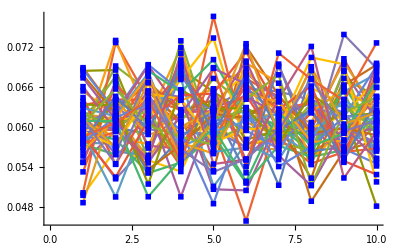

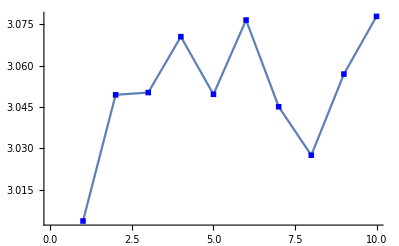

```mathematica
ListPlot[Is//Transpose,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListPlot[Total[Is//Transpose],Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

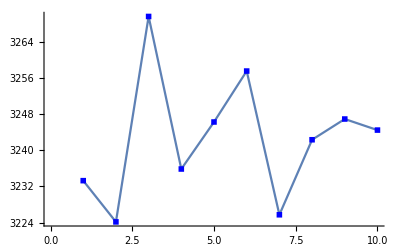

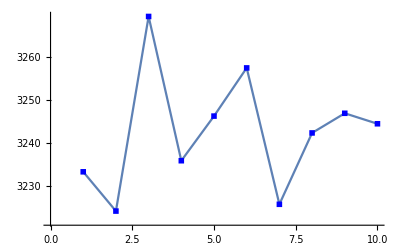

```mathematica
ListPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
ListLogPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

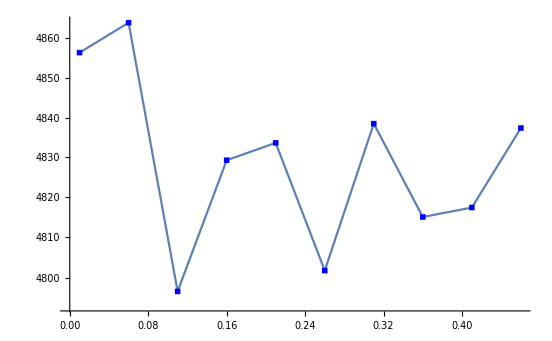

```mathematica
ListLogPlot[tms,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

```mathematica
x=Transpose[Ivsg2s];
y=Accumulate[x];
Manipulate[ListPlot[y[[i]]/i,Joined->True,PlotMarkers->{"X"}],{i,1,Length[y],1}]
```

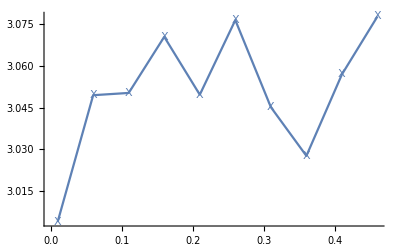

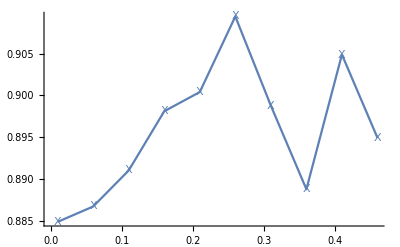

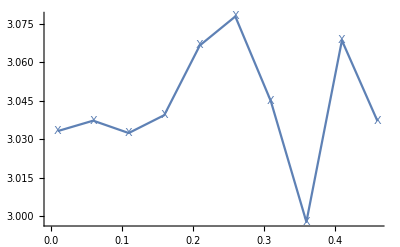

```mathematica
ListPlot[{Ivsg},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg2},Joined->True,PlotMarkers->{"X"}]
ListPlot[{Ivsg3},Joined->True,PlotMarkers->{"X"}]
```